```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\spectro

```mathematica
fit=A/((x-X)^2+b^2)/.{A->"4.2780000"×10^("7"),X->408.4,b->54.25};
center=408.4(*the lorentzian center*)
```

408.4

```mathematica
lorentzian=Flatten[Import["lorentzian.csv","Table"]];
```

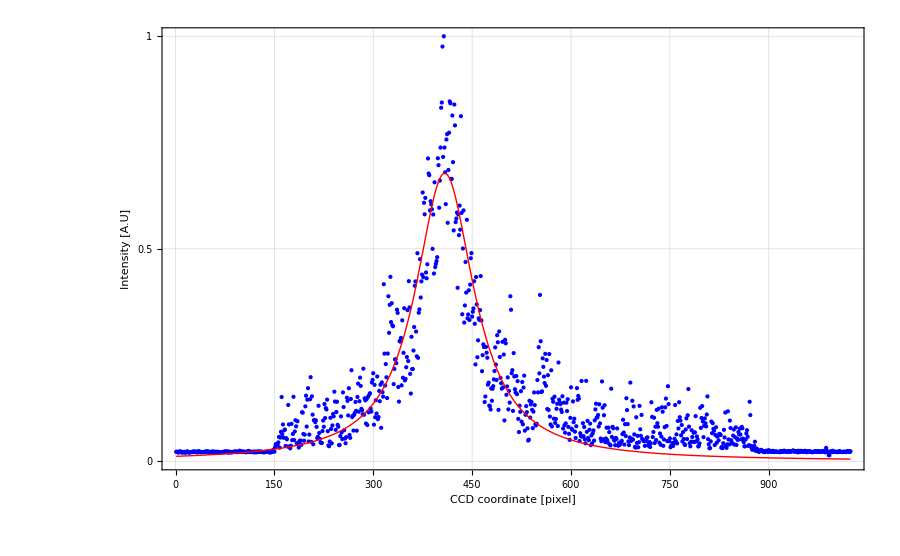

```mathematica
plot=Show[{ListPlot[lorentzian,PlotRange->All,PlotStyle->{Blue,PointSize[Medium]}],Plot[fit,{x,1,1024},PlotStyle->{Red,Thick(*ness[0.005]*)},PlotRange->All]},Frame->True,GridLines->Automatic,FrameLabel->{{"Intensity\n[A.U]",None},{"CCD coordinate [pixel]","Wavelength [nm]"}}
,FrameTicks->{{{0,{Max[lorentzian],1},{Max[lorentzian]/2,0.5}},None},{Automatic,MapAt[NumberForm[#,4]&,Thread[{Table[408.3+653.3/2 j,{j,-1.5,2,0.5}],Table[653.3+653.3/40 j,{j,-1.5,2,0.5}]}],{All,{2}}]}}
,LabelStyle->Directive[(*Bold,*)Black, 25],ImageSize->900]
```